```mathematica
(*This cell gives the matrix K from the proof of Theorem 5.2 in the case that r=5. Note that since each value of r' that we consider is at most 5, this is sufficient. The function "getColumnNumber" maps an edge of a graph (whose edges correspond to entries in a 3x5 matrix) to its corresponding column of K. The method "getCorrespondingSubmatrix" maps a whole graph to its corresponding column submatrix of K. K35Incidence matrix is the incidence matrix of the complete bipartite graph on partite sets of size 3 and 5. The method "get2CoreKernel" maps a bipartite graph on partite sets of size 3 and 5 to a matrix spanning the kernel of its incidence matrix. The claim is that for any possible 2-core G discussed, the rank of the matrix getCorrespondingSubmatrix[G].get2CoreKernel[G] is 3.*)
K={{t[1,1],t[1,2],t[1,3],t[1,4],t[1,5],1/t[1,1],1/t[1,2],1/t[1,3],1/t[1,4],1/t[1,5],0,0,0,0,0},
{t[2,1],t[2,2],t[2,3],t[2,4],t[2,5],0,0,0,0,0,1/t[2,1],1/t[2,2],1/t[2,3],1/t[2,4],1/t[2,5]},
{0,0,0,0,0,t[2,1]/t[1,1],t[2,2]/t[1,2],t[2,3]/t[1,3],t[2,4]/t[1,4],t[2,5]/t[1,5],t[1,1]/t[2,1],t[1,2]/t[2,2],t[1,3]/t[2,3],t[1,4]/t[2,4],t[1,5]/t[2,5]}};
K35IncidenceMatrix={
{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1},
{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0},
{0,1,0,0,0,0,1,0,0,0,0,1,0,0,0},
{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0},
{0,0,0,1,0,0,0,0,1,0,0,0,0,1,0},
{0,0,0,0,1,0,0,0,0,1,0,0,0,0,1}};
getColumnNumber[edge_]:=Switch[edge,"R1"<->"C1",1,"R1"<->"C2",2,"R1"<->"C3",3,"R1"<->"C4",4,"R1"<->"C5",5,"R2"<->"C1",6,"R2"<->"C2",7,"R2"<->"C3",8,"R2"<->"C4",9,"R2"<->"C5",10,"R3"<->"C1",11,"R3"<->"C2",12,"R3"<->"C3",13,"R3"<->"C4",14,"R3"<->"C5",15];
getCorrespondingSubmatrix[G_]:=K[[All,Map[getColumnNumber,EdgeList[G]]]];
get2CoreKernel[G_]:=Transpose[NullSpace[K35IncidenceMatrix[[All,Map[getColumnNumber,EdgeList[G]]]]]];
fontSize=12;
```

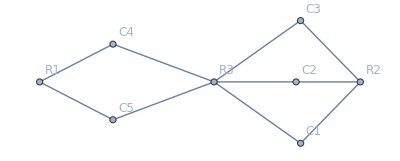
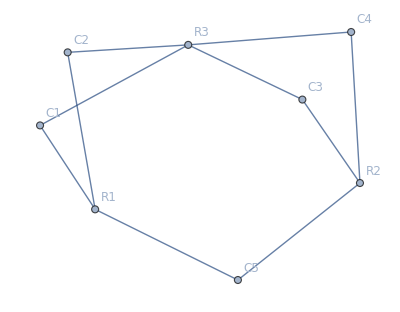
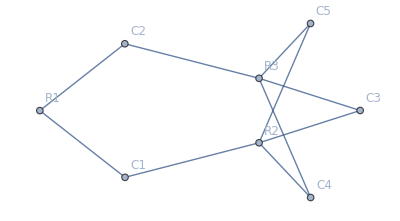

{3,3,3}

```mathematica
twoCoreEdgeSets = {{1 <-> 7, 1 <-> 8, 2 <-> 4, 2 <-> 5, 2 <-> 6, 3 <-> 4, 3 <-> 5, 3 <-> 6, 3 <-> 7, 3 <-> 8}, {1 <-> 4, 1 <-> 5, 1 <-> 8, 2 <-> 6, 2 <-> 7, 2 <-> 8, 3 <-> 4, 3 <-> 5, 3 <-> 6, 3 <-> 7}, {1 <-> 4, 1 <-> 5, 2 <-> 4, 2 <-> 6, 2 <-> 7, 2 <-> 8, 3 <-> 5, 3 <-> 6, 3 <-> 7, 3 <-> 8}};
twoCores=Map[Graph,twoCoreEdgeSets];
vertexRelableing={1->"R1",2->"R2",3->"R3",4->"C1",5->"C2",6->"C3",7->"C4",8->"C5"};
twoCores=Map[Function[G,VertexReplace[G,vertexRelableing]],twoCores];
(*The above line changes the names of the vertices so that their correspondence to entries of a 3x5 matrix is clear*)
Map[Function[G,Graph[G,VertexLabels->"Name",VertexLabelStyle->Directive[fontSize]]],twoCores]
Map[Function[G,MatrixRank[getCorrespondingSubmatrix[G].get2CoreKernel[G]]],twoCores]
(*The above line should output a list of 3s*)
```

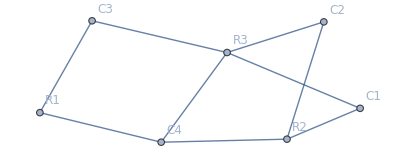
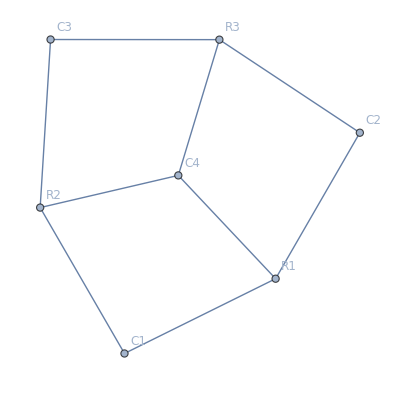

{3,3}

```mathematica
twoCoreEdgeSets={{1<->6,1<->7,2<->4,2<->5,2<->7,3<->4,3<->5,3<->6,3<->7},{1<->4,1<->5,1<->7,2<->4,2<->6,2<->7,3<->5,3<->6,3<->7}};
twoCores=Map[Graph,twoCoreEdgeSets];
Map[EdgeList,twoCores];
vertexRelableing={1->"R1",2->"R2",3->"R3",4->"C1",5->"C2",6->"C3",7->"C4"};
(*The above line changes the names of the vertices so that their correspondence to entries of a 3x5 matrix is clear*)
twoCores=Map[Function[G,VertexReplace[G,vertexRelableing]],twoCores];
Map[Function[G,Graph[G,VertexLabels->"Name",VertexLabelStyle->Directive[fontSize]]],twoCores]
Map[Function[G,MatrixRank[getCorrespondingSubmatrix[G].get2CoreKernel[G]]],twoCores]
(*The above line should output a list of 3s*)
```

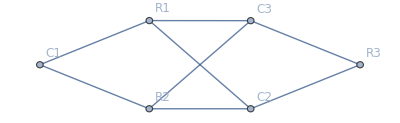

{3}

```mathematica
twoCoreEdgeSets={{1<->4,1<->5,1<->6,2<->4,2<->5,2<->6,3<->5,3<->6}};
twoCores=Map[Graph,twoCoreEdgeSets];
vertexRelableing={1->"R1",2->"R2",3->"R3",4->"C1",5->"C2",6->"C3"};
(*The above line changes the names of the vertices so that their correspondence to entries of a 3x5 matrix is clear*)
twoCores=Map[Function[G,VertexReplace[G,vertexRelableing]],twoCores];
Map[Function[G,Graph[G,VertexLabels->"Name",VertexLabelStyle->Directive[fontSize]]],twoCores]
Map[Function[G,MatrixRank[getCorrespondingSubmatrix[G].get2CoreKernel[G]]],twoCores]
(*The above line should output a list of 3s*)
```

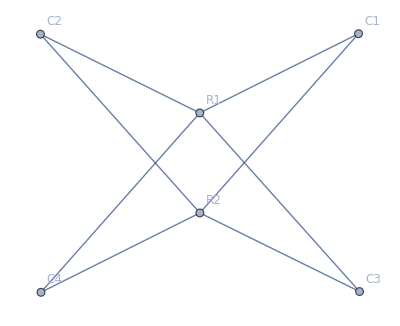

{3}

```mathematica
twoCoreEdgeSets={{1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->5,2<->6}};
twoCores=Map[Graph,twoCoreEdgeSets];
vertexRelableing={1->"R1",2->"R2",3->"C1",4->"C2",5->"C3",6->"C4"};
(*The above line changes the names of the vertices so that their correspondence to entries of a 3x5 matrix is clear*)
twoCores=Map[Function[G,VertexReplace[G,vertexRelableing]],twoCores];
Map[Function[G,Graph[G,VertexLabels->"Name",VertexLabelStyle->Directive[fontSize]]],twoCores]
Map[Function[G,MatrixRank[getCorrespondingSubmatrix[G].get2CoreKernel[G]]],twoCores]
(*The above line should output a list of 3s*)
```